```mathematica
ClearAll["Global`*"];
(*W „wesołym miasteczku” zbudowano „diabelską pętlę” o promieniu R. Jaka powinna być minimalna wysokość H zjeżdżalni dla wózków, aby
wraz z pasażerami mijały one bezpiecznie (nie odrywały się od toru)
najwyższy punkt pętli? Sporządzić wykres obrazujący zależność H od
R dla R zmieniającego się w zakresie od 5 m do 10 m.*)

Fod=(m×v^2)/R;
Fg=m×g;
```

```mathematica
Ep1=m×g×H;
Ep2=m×g×(2×R);
Ek2=(m×v^2)/2;
```

```mathematica
r1=Solve[{Fod==Fg, Ep1-Ep2==Ek2},{H,v}]
```

{{H→(5 R)/2,v→-√g √R},{H→(5 R)/2,v→√g √R}}

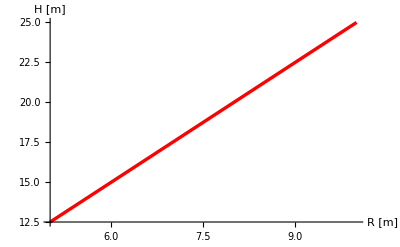

```mathematica
Plot[H/.r1[[1,1]],{R,5,10},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"R [m]","H [m]"}]
```